```mathematica
rawdata=Import["D:\\Circuit-Experiment\\wjj\\12\\12_data.xlsx"];
```

```mathematica
Us=3;
```

```mathematica
Do[{R[i],c[i],L[i]}={rawdata[[i]][[15,3]],rawdata[[i]][[15,9]]/10^6,rawdata[[i]][[15,6]]/10^3},{i,1,4}];
```

```mathematica
Do[dataRvsf[i]=rawdata[[i]][[3;;11,{4,5}]],{i,2,4}];
Do[dataCvsf[i]=rawdata[[i]][[3;;11,{4,7}]],{i,2,4}];
Do[dataLvsf[i]=rawdata[[i]][[3;;11,{4,6}]],{i,2,4}];
Do[dataXvsf[i]=rawdata[[i]][[3;;11,{4,8}]],{i,2,4}];
```

```mathematica
Do[nlmRvsf[i]=NonlinearModelFit[dataRvsf[i],(3 R[i])/(√((2 f l π-1/(2π f c[i]))^2+(R[i]+r)^2)),{r,{l,0.005}},f,MaxIterations->1000],{i,2,4}];
Do[nlmLvsf[i]=NonlinearModelFit[dataLvsf[i],(3 √((2 f l π)^2+rl^2))/(√((2 f l π-1/(2π f c[i]))^2+(R[i]+r+rl)^2)),{r,{l,0.005},{rl,30}},f,MaxIterations->1000],{i,2,4}];
Do[nlmCvsf[i]=NonlinearModelFit[dataCvsf[i],(3 √((1/(2π f c[i]))^2+rc^2))/(√((2 f l π-1/(2π f c[i]))^2+(R[i]+r+rc)^2)),{r,{l,0.01},rc},f,MaxIterations->1000],{i,2,4}];
Do[nlmXvsf[i]=NonlinearModelFit[dataXvsf[i],(3 √((2 f l π-1/(2π f c[i]))^2+rcl^2))/(√((2 f l π-1/(2π f c[i]))^2+(R[i]+rs+rcl)^2)),{rs,{l,0.01},rcl},f,MaxIterations->1000],{i,2,4}];
```

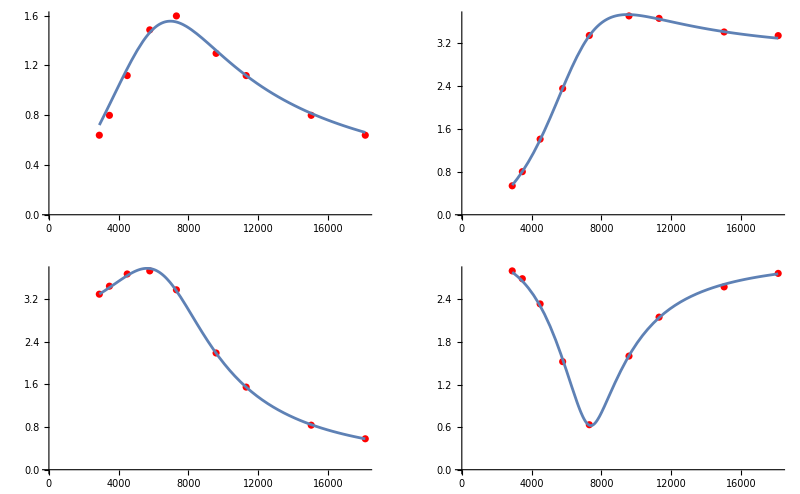

```mathematica
GraphicsGrid[
{
{
Show[ListPlot[dataRvsf[4],PlotStyle->Red],Plot[nlmRvsf[4][f],{f,2890.,18140.},PlotRange->All]],
Show[ListPlot[dataLvsf[4],PlotStyle->Red],Plot[nlmLvsf[4][f],{f,2890.,18140.},PlotRange->All]]
},{
Show[ListPlot[dataCvsf[4],PlotStyle->Red],Plot[nlmCvsf[4][f],{f,2890.,18140.},PlotRange->All]],
Show[ListPlot[dataXvsf[4],PlotStyle->Red],Plot[nlmXvsf[4][f],{f,2890.,18140.},PlotRange->All]]
}
}
]
```

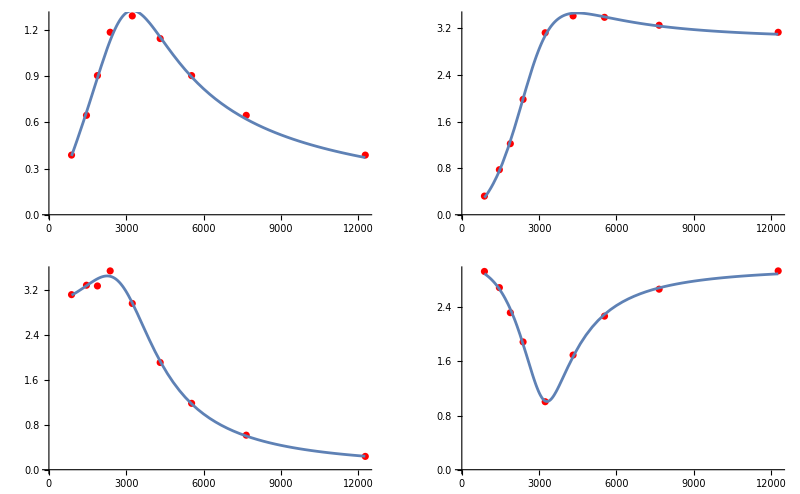

```mathematica
GraphicsGrid[
{
{
Show[ListPlot[dataRvsf[2],PlotStyle->Red],Plot[nlmRvsf[2][f],{f,878.,12278.},PlotRange->All]],
Show[ListPlot[dataLvsf[2],PlotStyle->Red],Plot[nlmLvsf[2][f],{f,878.,12278.},PlotRange->All]]
},{
Show[ListPlot[dataCvsf[2],PlotStyle->Red],Plot[nlmCvsf[2][f],{f,878.,12278.},PlotRange->All]],
Show[ListPlot[dataXvsf[2],PlotStyle->Red],Plot[nlmXvsf[2][f],{f,878.,12278.},PlotRange->All]]
}
}
]
```

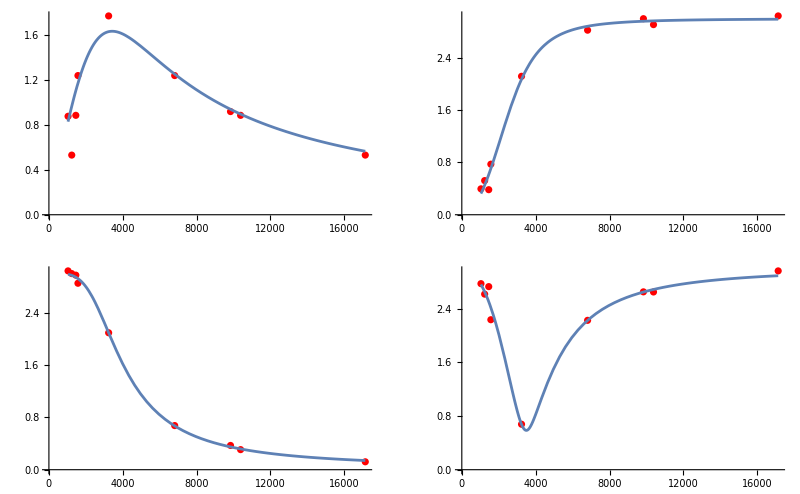

```mathematica
GraphicsGrid[
{
{
Show[ListPlot[dataRvsf[3],PlotStyle->Red],Plot[nlmRvsf[3][f],{f,1037.,17137.},PlotRange->All]],
Show[ListPlot[dataLvsf[3],PlotStyle->Red],Plot[nlmLvsf[3][f],{f,1037.,17137.},PlotRange->All]]
},{
Show[ListPlot[dataCvsf[3],PlotStyle->Red],Plot[nlmCvsf[3][f],{f,1037.,17137.},PlotRange->All]],
Show[ListPlot[dataXvsf[3],PlotStyle->Red],Plot[nlmXvsf[3][f],{f,1037.,17137.},PlotRange->All]]
}
}
]
```